Plot[current[t],{t,0,10}, Frame→True]

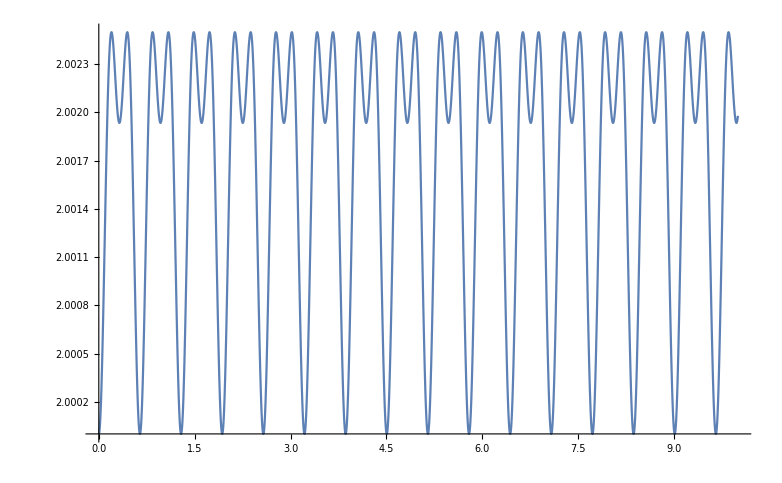

```mathematica
SolN[g_,Ω_,J_,T_,x0_,y0_,z0_]:=NDSolve[{x'[t]==ⅈ*g*Ω(2ⅈ Im[z[t]*y[t]+g*x[t]]),y'[t]==ⅈ*g*Ω(-2ⅈ Im[z[t]*x[t]+g*y[t]]), z'[t]==ⅈ(Ω*z[t]-g*T*x[t]+g*J*y[t]),x[0]==x0,y[0]==y0, z[0]==z0},{x,y,z},{t,0,30}];
g=1/3;
Ω=5;
J=0;
T=-31.6;
x0=0.1;
y0=2;
z0=0;
s=SolN[g,Ω,J,T,x0,y0,z0];
sina=First[x/.s];
cosa=First[y/.s];
current=J*cosa[#]-T*sina[#]&;
"Plot[current[t],{t,0,10}, Frame→True]"
Plot[cosa[t], {t,0,10}]
```

```mathematica
SolN[g_,Ω_,J_,T_,x0_,y0_,z0_]:=NDSolve[{x'[t]==ⅈ*g*Ω(2ⅈ Im[z[t]*y[t]+g*x[t]]),y'[t]==ⅈ*g*Ω(-2ⅈ Im[z[t]*x[t]+g*y[t]]), z'[t]==ⅈ(Ω*z[t]-g*T*x[t]+g*J*y[t]),c[t]==(y[t]*J)-(x[t]*T), x[0]==x0,y[0]==y0, z[0]==z0, c[0]== y0*J-x0*T},{x,y,z, c},{t,0,1000}];
```

```mathematica
"Plot[Evaluate[x[t]/.s],{t,0,30},PlotRange→All, Frame→True]"
```